```mathematica
(*why doesn't the ensemble sum over different combinations of Subscript[Q, 1] and Subscript[Q, 2] aswell?*)
(*Replace Q and g constants by Q^2 and g^2?*)
(*idea for analytical manipulation: do τ integral first?*)

MargaretdEdx5Points=Import["C:\\Users\\jose2\\Desktop\\Werk\\Técnico\\6 Ano 1 Semestre\\Liliana_Pablo\\Graph Reader\\Nova pasta\\dEdx_Margaret_v2.csv"]
dEdx5=Interpolation[MargaretdEdx5Points,InterpolationOrder->1];
MargaretQHat5Points=Import["C:\\Users\\jose2\\Desktop\\Werk\\Técnico\\6 Ano 1 Semestre\\Liliana_Pablo\\Graph Reader\\qhat_5_v2.csv"];
QHat5=Interpolation[MargaretQHat5Points,InterpolationOrder->1];
MargaretQHat1Points=Import["C:\\Users\\jose2\\Desktop\\Werk\\Técnico\\6 Ano 1 Semestre\\Liliana_Pablo\\Graph Reader\\qhat_1_v2.csv"];
QHat1=Interpolation[MargaretQHat1Points,InterpolationOrder->1];

GeVtofm=0.1973; (*1 GeV = GeVtofm / 1 fm -- should use more algarisms?*)
Subscript[v, perp]=1.0; (*adimensional*)
Subscript[v, paral]=0; (*adimensional*)
v=√(Subscript[v, perp]^2+Subscript[v, paral]^2); (*adimensional - should v always equal 1?*)
Subscript[N, c]=3;
g=1.0; (*adimensional*)
T=0.150; 
Subscript[Q, 1]=2.0;  (*GeV*)
Subscript[Q, 2]=2.0;(*GeV*)

r2[τ_,τʹ_,φ_,ϕ_]:=(Subscript[v, perp]*(τ-τʹ)+(τʹ*Cos[φ]-τ*Cos[ϕ]))^2+(τʹ*Sin[φ]-τ*Sin[ϕ])^2(*GeV^-2*)
GGBW[x_,Q_]:=Q^2/(g^2*Subscript[N, c])*(1-Exp[-x])/x(*GeV^2*) 
GBWArg[r2_,Q_]:=(Q^2*r2)/4(*adimensional*)

(*STOPPING POWER*)
IntegrandStoppingPower[τ_,τʹ_,φ_,ϕ_]:=GGBW[GBWArg[r2[τ,τʹ,φ,ϕ],Subscript[Q, 1]],Subscript[Q, 1]]*GGBW[GBWArg[r2[τ,τʹ,φ,ϕ],Subscript[Q, 2]],Subscript[Q, 2]]*(Subscript[v, paral]^2+Subscript[v, perp]^2*Sin[φ]*Sin[ϕ])(*GeV^4*)
stoppingPower[τ_]:=-1/(v*T)*g^4/4*(Subscript[N, c]^2-1)*NIntegrate[IntegrandStoppingPower[τ,τʹ,φ,ϕ],{φ,0,2π},{ϕ,0,2π},{τʹ,0,τ}] (*GeV^2*)

(*QHAT*)
IntegrandQhat[τ_,τʹ_,φ_,ϕ_]:=GGBW[GBWArg[r2[τ,τʹ,φ,ϕ],Subscript[Q, 1]],Subscript[Q, 1]]*GGBW[GBWArg[r2[τ,τʹ,φ,ϕ],Subscript[Q, 2]],Subscript[Q, 2]]*(Subscript[v, paral]^2*Cos[ϕ-φ]+Subscript[v, perp]^2*(Cos[φ]*Cos[ϕ]+1))(*GeV^4*)
Qhat[τ_]:=g^4/4*(Subscript[N, c]^2-1)*(1+v^2)/v^3*NIntegrate[IntegrandQhat[τ,τʹ,φ,ϕ],{φ,0,2π},{ϕ,0,2π},{τʹ,0,τ}] (*GeV^3*)
```

{{0.00122,0.00098},{0.00204,0.00098},{0.00285,0.00272},{0.00366,0.00272},{0.00448,0.00272},{0.00543,0.00446},{0.00624,0.00332},{0.00705,0.00362},{0.00787,0.00451},{0.00868,0.00451},{0.0095,0.00451},{0.01044,0.00715},{0.01126,0.00925},{0.01207,0.00985},{0.01289,0.01254},{0.0137,0.01403},{0.01451,0.01672},{0.01533,0.01971},{0.01614,0.02211},{0.01695,0.0251},{0.01777,0.02809},{0.01858,0.03167},{0.01939,0.03556},{0.02021,0.03975},{0.02102,0.04393},{0.02184,0.04872},{0.02265,0.0538},{0.02346,0.05918},{0.02428,0.06486},{0.02509,0.07054},{0.0259,0.07712},{0.02672,0.0834},{0.02753,0.08998},{0.02834,0.09775},{0.02916,0.10493},{0.02997,0.1127},{0.03079,0.12108},{0.0316,0.12945},{0.03241,0.13782},{0.03323,0.14649},{0.03404,0.15576},{0.03485,0.16503},{0.03567,0.174},{0.03648,0.18357},{0.0373,0.19374},{0.03811,0.20301},{0.03892,0.21317},{0.03974,0.22274},{0.04055,0.23321},{0.04136,0.24247},{0.04218,0.25264},{0.04299,0.26221},{0.0438,0.27208},{0.04462,0.28135},{0.04543,0.29062},{0.04625,0.29929},{0.04706,0.30796},{0.04787,0.31603},{0.04869,0.32381},{0.0495,0.33068},{0.05031,0.33726},{0.05113,0.34324},{0.05194,0.34832},{0.05275,0.35281},{0.05357,0.3558},{0.05438,0.35789},{0.0552,0.35849},{0.05601,0.35939},{0.05682,0.35789},{0.05764,0.3555},{0.05845,0.35131},{0.05926,0.34563},{0.06008,0.33756},{0.06089,0.32829},{0.0617,0.31633},{0.06252,0.30287},{0.06333,0.28643},{0.06415,0.26759},{0.06489,0.24774},{0.06557,0.22657},{0.06625,0.2054},{0.06686,0.18252},{0.0674,0.16099},{0.06794,0.13902},{0.06842,0.1157},{0.06889,0.09327},{0.06937,0.06905},{0.06977,0.04632},{0.07018,0.02181},{0.07052,0.00303},{0.07086,-0.02015},{0.07126,-0.04517},{0.07147,-0.06311},{0.07179,-0.08416},{0.07201,-0.10677},{0.07228,-0.12605}}

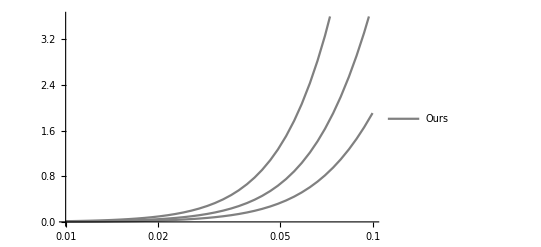

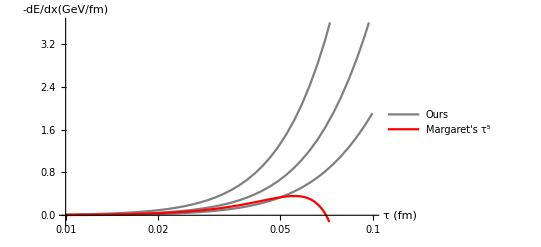

-Graphics-

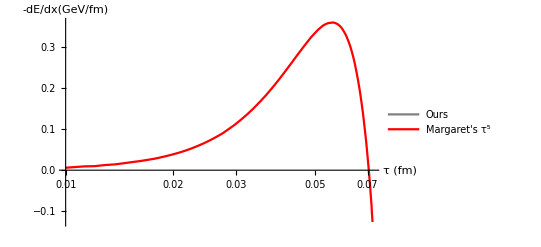

```mathematica
p1=LogLinearPlot[{-stoppingPower[τ/GeVtofm], -stoppingPower[τ/GeVtofm]*2, -stoppingPower[τ/GeVtofm]/2}*GeVtofm,{τ,0.01,0.1},PlotPoints->40,MaxRecursion->0,PlotLegends->{"Ours"},PlotStyle->{{Thick,Gray},{Thick,Black},{Thick,Gray}},Filling->{3->{2}}]
Show[p1,LogLinearPlot[dEdx5[τ],{τ,0.01,0.07228},PlotLegends->{"Margaret's τ^5"},PlotStyle->{Thick,Red}],AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotRange->Automatic](*GeV/fm as function of fm*)
```

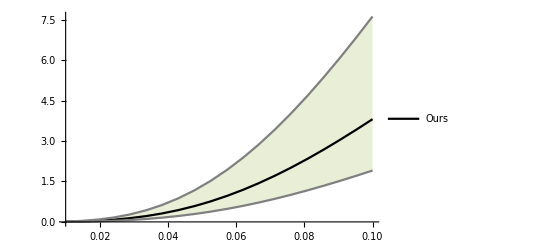

```mathematica
p2=Plot[{-stoppingPower[τ/GeVtofm]*GeVtofm,-stoppingPower[τ/GeVtofm]*GeVtofm*2,-stoppingPower[τ/GeVtofm]*GeVtofm/2},{τ,0.01,0.1},PlotPoints->20,MaxRecursion->0,PlotStyle->{{Thick,Black},{Thick,Gray},{Thick,Gray}},PlotLegends->{"Ours"},Filling->{3->{2}}]
```

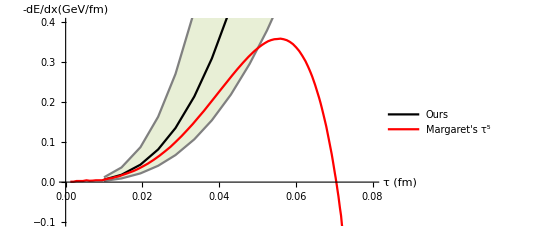

```mathematica
Show[p2,Plot[dEdx5[τ],{τ,0.00122,0.07228},PlotLegends->{"Margaret's τ^5"},PlotStyle->{Thick,Red}],AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotRange->{{0,0.08},{-0.1,0.4}},AxesOrigin->{0,0}]
```

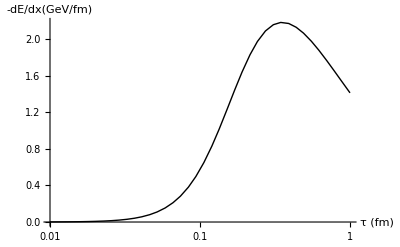

```mathematica
LogLinearPlot[-stoppingPower[τ/GeVtofm]*GeVtofm,{τ,0.01,1},PlotPoints->40,MaxRecursion->0,AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotStyle->{Thick,Black}]
```

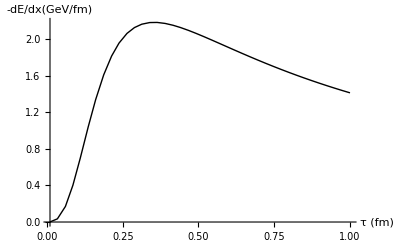

```mathematica
Plot[-stoppingPower[τ/GeVtofm]*GeVtofm,{τ,0.01,1},PlotPoints->40,MaxRecursion->0,AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotStyle->{Thick,Black}]
```

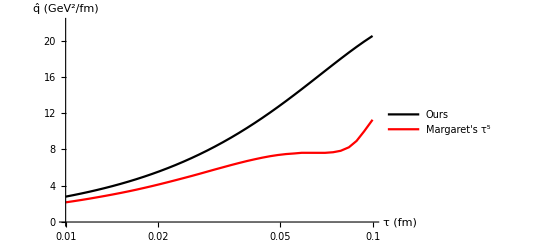

```mathematica
LogLinearPlot[{Qhat[τ/GeVtofm]*GeVtofm(*,QHat1[τ]*),QHat5[τ]},{τ,0.01,0.1},PlotPoints->40,MaxRecursion->0,AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"},PlotRange->{0,22},PlotLegends->{"Ours"(*,"Margaret's τ^1"*),"Margaret's τ^5"},PlotStyle->{{Thick,Black}(*,{Thick,Blue}*),{Thick,Red}}] (*GeV^2/fm as function of fm*)
```

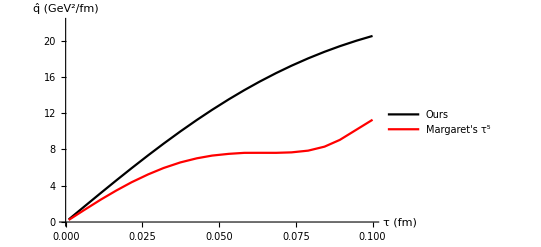

```mathematica
Plot[{Qhat[τ/GeVtofm]*GeVtofm(*,QHat1[τ]*),QHat5[τ]},{τ,0.001,0.1},PlotPoints->20,MaxRecursion->0,AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"},PlotRange->{0,22},PlotLegends->{"Ours"(*,"Margaret's τ^1"*),"Margaret's τ^5"},PlotStyle->{{Thick,Black}(*,{Thick,Blue}*),{Thick,Red}}]
```

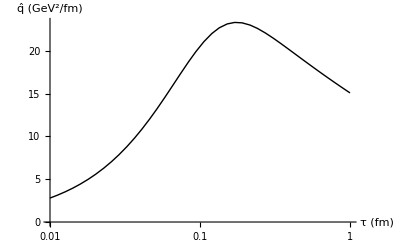

```mathematica
LogLinearPlot[Qhat[τ/GeVtofm]*GeVtofm,{τ,0.01,1},PlotPoints->40,MaxRecursion->0,AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"},PlotStyle->{Thick,Black}]
```

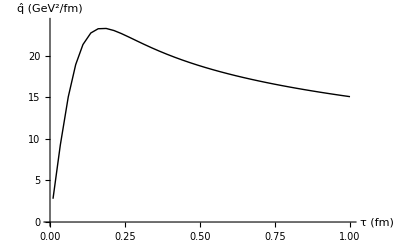

```mathematica
Plot[Qhat[τ/GeVtofm]*GeVtofm,{τ,0.01,1},PlotPoints->40,MaxRecursion->0,AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"},PlotStyle->{Thick,Black},PlotRange->{0,24}]
```

```mathematica
(*linPointsListdEdx=
ListLinePlot[Table[{i,With[{y=Sin[π i]},Around[y,.05 y]]},{i,0,1,0.01}],IntervalMarkers->"Bands",PlotTheme->"Scientific"]*)
```

```mathematica
Clear["Global`*"]
```